```mathematica
ClearAll["Global`*"];
<<NumericalDifferentialEquationAnalysis`
```

#### Optical properties

#### Matrix size

```mathematica
M=128;
```

#### Absorption&scattering coefficients

```mathematica
μs=9000;
μa=1000;
```

#### Albedo

```mathematica
a=μs/(μs+μa);
```

#### Optical thickness

```mathematica
d=0.1×10^-3;
τ=d×(μs+μa);
```

#### Anisotropy

```mathematica
g=0.9;
```

#### Refractive index

```mathematica
n=1.5;
nglass=1.5;
```

### Integrating spheres properties

#### Sphere diameter

```mathematica
d=7.×10^-3;
r=d/2;
```

#### Quadrature angles

Total internal reflection

```mathematica
θ [n_]= ArcSin[1.0/n];
```

Critical cosine

```mathematica
νc[n_]=Cos[θ[n]];
```

Gauss (0<θ<ν_c)

```mathematica
gauss=GaussianQuadratureWeights[M/2,0,νc[n]];
νGauss=gauss[[All,1]];
wGauss=gauss[[All,2]];
```

Radau (ν_c<θ<1)

```mathematica
cachedLegendreP[k_,x_]:=cachedLegendreP[k,x]=LegendreP[k,x];
```

```mathematica
Radau[x_,m_]=(cachedLegendreP[m/2-1,x]+cachedLegendreP[m/2,x])/(1+x);
```

```mathematica
Der[x_,m_]=D[cachedLegendreP[m/2,x],x];
```

```mathematica
RadauRoots=Sort[Flatten[N[{x/.Solve[Radau[x,M]==0,x], -1}]],Greater];
```

```mathematica
νRadau=ParallelTable[N[(1+νc[n])/2-(1-νc[n])/2×RadauRoots[[j]]],{j,M/2}];
```

```mathematica
wRadau=Flatten[{ParallelTable[(1-νc[n])/(2 (1-RadauRoots[[j]]) (Der[RadauRoots[[j]],M-2])^2),{j,M/2-1}],{(1-νc[n])/(M/2)^2}}];
```

#### Final quadrature angles and weights

```mathematica
ν=Flatten[{νGauss,νRadau}];
w = Flatten[{wGauss,wRadau}];
ClearAll[RadauRoots,GaussLRoots,νGauss,νRadau,wGauss,wRadau];
```

```mathematica
anglesRad=ParallelTable[ArcCos[ν[[i]]],{i,Length[ν]}];
anglesDeg=ParallelTable[(anglesRad[[i]] 180)/π,{i,Length[ν]}];
```

### The Redistribution Function

#### δ-M method

```mathematica
SuperStar[τ]=(1-a g^M)τ
```

0.999999

```mathematica
as=a(1-g^M)/(1-a g^M)
```

0.9

Optical thickness of starting layer: Δτ^*<ν_1 (min ν)

We want Δτ^*×2^n1=τ^*

```mathematica
Off[NSolve::ifun]
n1=Ceiling[x/.NSolve[SuperStar[τ]==Min[ν] 2^x,x,Reals][[1]]]
```

12

```mathematica
Δτs=SuperStar[τ]/2^n1
```

0.00024414

```mathematica
Δτ=Δτs/(1-a g^M);
```

#### Heyney-Greenstein phase function

```mathematica
SuperStar[χ][k_]:=SuperStar[χ][k]=(g^k-g^M)/(1-g^M);
```

```mathematica
PPmatrix=ConstantArray[0.,{M, M}];
PPmatrix[[1,All]]=1.;
PPmatrix[[2,All]]=ν;
Do[Do[PPmatrix[[nn,j]]=((2nn-3) ν[[j]] PPmatrix[[nn-1,j]]-(nn-2) PPmatrix[[nn-2,j]])/(nn-1),{nn,3,M}],{j,M}];
PNmatrix=ParallelTable[(-1)^(nn-1) PPmatrix[[nn,j]],{nn,1,M},{j,1,M}];
```

```mathematica
hpp=ConstantArray[0.,{M, M}];
hpm=ConstantArray[0.,{M, M}];
If[g==0,
hpp=ConstantArray[1.,{M, M}];
hpm=ConstantArray[1.,{M, M}];
,
Do[Do[hpp[[i,j]]=Sum[(2k+1) SuperStar[χ][k]PPmatrix[[k+1,i]] PPmatrix[[k+1,j]],{k,0,M-1}],{j,i,M}],{i,M}];
Do[Do[hpp[[j,i]]=hpp[[i,j]],{j,i+1,M}],{i,M}];
Do[Do[hpm[[i,j]]=Sum[(2k+1) SuperStar[χ][k]PPmatrix[[k+1,i]] PNmatrix[[k+1,j]],{k,0,M-1}],{j,i,M}],{i,M}];
Do[Do[hpm[[j,i]]=hpm[[i,j]],{j,i+1,M}],{i,M}];
];
```

```mathematica
(*ClearAll[cachedLegendreP,PPmatrix,PNmatrix];*)
```

#### Layer Initialiation

```mathematica
EE=IdentityMatrix[M];
```

```mathematica
B=ParallelTable[(as Δτs w[[j]])/(4 ν[[i]]) hpm[[i,j]],{i,M},{j,M}];
```

```mathematica
A=ParallelTable[i,j Δτs/(2 ν[[i]])-(as Δτs w[[j]])/(4 ν[[i]])hpp[[i,j]],{i,M},{j,M}];
```

```mathematica
Inv=Inverse[EE+A];
```

```mathematica
G=Inverse[EE+A-B.Inv.B];
```

```mathematica
R=2.G.B.Inv;
```

```mathematica
T=2.G-EE;
```

```mathematica
(*ClearAll[A,B,G,Inv,hpp,hpm];*)
```

```mathematica
twoaw=2 ν w;
```

```mathematica
Rd1=ParallelTable[R[[i,j]]/twoaw[[j]],{i,M},{j,M}];
Td1=ParallelTable[T[[i,j]]/twoaw[[j]],{i,M},{j,M}];
```

#### Doubling until desired thickness is reached

```mathematica
newE=DiagonalMatrix[1./twoaw];
star=DiagonalMatrix[twoaw];
```

Now I’ll try to avoid recursion here...

```mathematica
Td2=ConstantArray[0.,{M,M}];
Rd2=ConstantArray[0.,{M,M}];
Td=List[Td1,Td2];
Rd=List[Rd1,Rd2];
```

```mathematica
For[i=1,i≤n1,i++,
If[EvenQ[i]==False,
Td[[2]]=Td[[1]].Inverse[newE-Rd[[1]].star.Rd[[1]]].Td[[1]];
Rd[[2]]=Td[[1]].Inverse[newE-Rd[[1]].star.Rd[[1]]].Rd[[1]].star.Td[[1]]+Rd[[1]];
,
Td[[1]]=Td[[2]].Inverse[newE-Rd[[2]].star.Rd[[2]]].Td[[2]];
Rd[[1]]=Td[[2]].Inverse[newE-Rd[[2]].star.Rd[[2]]].Rd[[2]].star.Td[[2]]+Rd[[2]];
];
];
```

R and T for desired optical thickness

```mathematica
If[EvenQ[n1]==True,
Rslab=Rd[[1]];
Tslab=Td[[1]];
,
Rslab=Rd[[2]];
Tslab=Td[[2]];
];
```

#### Fresnel reflection & boundary conditions

```mathematica
νt[ni_,nt_,νi_]=√(1-(ni/nt)^2 (1-νi^2));
FresnelR[νi_,ni_,nt_]=1/2 ((nt νi-ni Re[νt[ni,nt,νi]])/(nt νi+ni Re[νt[ni,nt,νi]]))^2+1/2 ((ni νi-nt Re[νt[ni,nt,νi]])/(ni νi+nt Re[νt[ni,nt,νi]]))^2;
Rbound=DiagonalMatrix[Chop[((FresnelR[ν,n,nglass]+FresnelR[νt[n,nglass,ν],nglass,1]-2×FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1])/(1-FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1]))× twoaw]];
Tbound=DiagonalMatrix[Chop[1-(FresnelR[ν,n,nglass]+FresnelR[νt[n,nglass,ν],nglass,1]-2×FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1])/(1-FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1])]];
```

#### Adding boundaries to the slab

```mathematica
T02=Chop[Tslab.Inverse[EE-Rbound.Rslab].Tbound];
R20=Chop[Tslab.Inverse[EE-Rbound.Rslab].Rbound.Tslab+Rslab];
```

```mathematica
T03=Chop[Tbound.Inverse[EE-R20.Rbound].T02];
R30=Chop[Tbound.Inverse[EE-R20.Rbound].R20.Tbound];
For[i=1,i≤M,i++,R30[[i,i]]+=Rbound[[i,i]]/twoaw[[i]]^2];
```

```mathematica
{Rc=Total[2 ν w R30[[M]]],
Tc=Total[2 ν w T03[[M]]]}
```

{0.0844457,0.764198}

#### Find light cones within border

```mathematica
angleBorder[Z_]=N[ArcTan[r/Z]]×180/Pi;
withinBorder[Z_,list_]:=Module[{j},j=1;While[anglesDeg[[j]]>angleBorder[Z],j++];Drop[list,j-2]];
anglesWB[Z_]:=Module[{list},If[Z==0,list=anglesDeg,list=withinBorder[Z,anglesDeg]];list]
```

#### Sum concerning only angles within border

```mathematica
RlastWB[Z_]:=Module[{list},If[Z==0,list=R30[[All,M]],list=withinBorder[Z,R30[[All,M]]]];list];
νWB[Z_]:=Module[{list},If[Z==0,list=ν,list=withinBorder[Z,ν]];list];
wWB[Z_]:=Module[{list},If[Z==0,list=w,list=withinBorder[Z,w]];list];
R30WB[Z_]:=Transpose[{RlastWB[Z],νWB[Z],wWB[Z]}];
```

```mathematica
TlastWB[Z_]:=Module[{list},If[Z==0,list=T03[[All,M]],list=withinBorder[Z,T03[[All,M]]]];list];
T03WB[Z_]:=Transpose[{TlastWB[Z],νWB[Z],wWB[Z]}];
```

```mathematica
zRef[Z_]:=Z+70×10^-3;
RcWB[Z_]:=Sum[Chop[2×R30WB[Z][[i,1]]×R30WB[Z][[i,2]]×R30WB[Z][[i,3]]],{i,1,Length[R30WB[Z]]-1}]
TcWB[Z_]:=Sum[Chop[2×T03WB[Z][[i,1]]×T03WB[Z][[i,2]]×T03WB[Z][[i,3]]],{i,1,Length[R30WB[Z]]}]
```

```mathematica
RvsZ=ConstantArray[0,{10,2}];
TvsZ=ConstantArray[0,{10,2}];
For[i=1,i≤10,i++,RvsZ[[i,1]]=(i-1)×0.004;RvsZ[[i,2]]=RcWB[(i-1)×0.01]];
For[i=1,i≤10,i++,TvsZ[[i,1]]=(i-1)×0.004;TvsZ[[i,2]]=TcWB[(i-1)×0.01]];
```

#### Graphs

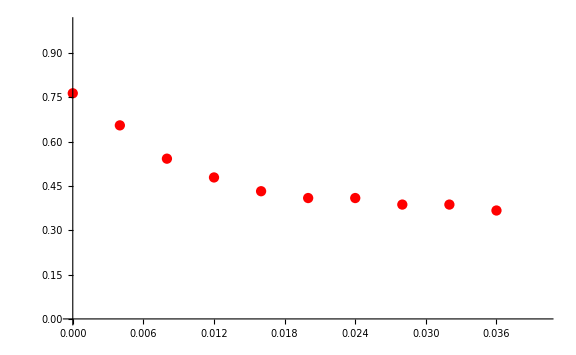
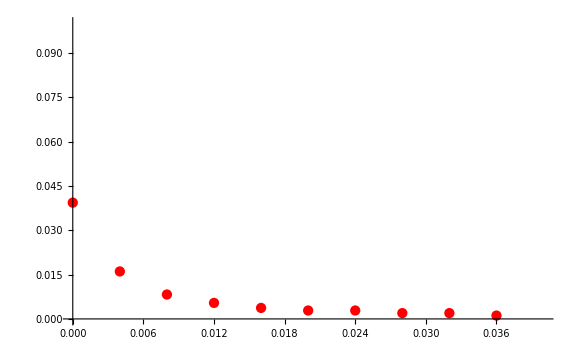

```mathematica
{Show[ListPlot[TvsZ,PlotStyle->Red],ImageSize->Large,PlotRange->{{0,0.04},{0,1}}],Show[ListPlot[RvsZ,PlotStyle->Red],ImageSize->Large,PlotRange->{{0,0.04},{0,0.1}}]}
```

```mathematica
{Rc,Tc}
```

{0.0844457,0.764198}